```mathematica
<<Radia`;
(* The x positions of each transport coil pair *)
MOTCoilXPos = 0;
OuterTransCoil1XPos = 2.375 * inch;
InnerTransCoil1XPos = 3.950*inch;
OuterTransCoil2XPos = 5.525 * inch;
InnerTransCoil2XPos = 7.100*inch;
OuterTransCoil3XPos = 8.675 * inch;
InnerTransCoil3XPos = 10.250*inch;
OuterTransCoil4XPos = 11.825 * inch;
InnerTransCoil4XPos = 13.400*inch;
OuterTransCoil5XPos = 14.975 * inch;
FinalCoilXPos = 17.35 * inch;
(* Inner transport coil *)
InnerTransCoilZPos = MOTCellSize/2 + MOTCellClearance
InnerTransCoilHeight = 0.25 * inch;
InnerTransCoilInnerR = 0.795 * inch;
InnerTransCoilOuterR = 1.575 * inch;
InnerTransCoilNTurns = 60;

(* Outer transport coil *)
OuterTransCoilZPos = MOTCoilZPos +MOTCoilHeight +QuadrupoleToOuterTransCoilClearance
OuterTransCoilHeight = 0.5 * inch;
OuterTransCoilInnerR = 0.795 * inch;
OuterTransCoilOuterR = 1.575 * inch;
OuterTransCoilNTurns = 60;
```

LinkObject::linkn: Argument LinkObject["C:\Program Files\Wolfram Research\Mathematica\11.2\AddOns\Applications\Radia\Radia.exe",13119,11] in LinkClose[LinkObject["C:\Program Files\Wolfram Research\Mathematica\11.2\AddOns\Applications\Radia\Radia.exe",13119,11]] has an invalid LinkObject number; the link may be closed.

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

21.59

29.718

```mathematica
CoilPair[x_, zpos_, innerRadius_, outerRadius_, height_,currentDensity_] :=radObjCnt[{
radObjRaceTrk[{x,0, zpos + height/2},{innerRadius, outerRadius},{0,0}, height, nSeg, currentDensity],
radObjRaceTrk[{x,0, -zpos - height/2},{innerRadius, outerRadius},{0,0}, height, nSeg, -currentDensity]
}];
curr = {0,0,0.1,1,0.1,0,0,0,0,0,0};
MOTCoils= CoilPair[MOTCoilXPos,MOTCoilZPos,MOTCoilInnerR, MOTCoilOuterR, MOTCoilHeight, MOTCoilJperAmp*curr[[1]]];
OuterTransCoils1= CoilPair[OuterTransCoil1XPos,OuterTransCoilZPos, OuterTransCoilInnerR, OuterTransCoilOuterR,OuterTransCoilHeight,OuterTransCoilJperAmp*curr[[2]]];
InnerTransCoils1= CoilPair[InnerTransCoil1XPos,InnerTransCoilZPos, InnerTransCoilInnerR, InnerTransCoilOuterR,InnerTransCoilHeight,InnerTransCoilJperAmp*curr[[3]]];
OuterTransCoils2= CoilPair[OuterTransCoil2XPos,OuterTransCoilZPos, OuterTransCoilInnerR, OuterTransCoilOuterR,OuterTransCoilHeight,OuterTransCoilJperAmp*curr[[4]]];
InnerTransCoils2= CoilPair[InnerTransCoil2XPos,InnerTransCoilZPos, InnerTransCoilInnerR, InnerTransCoilOuterR,InnerTransCoilHeight,InnerTransCoilJperAmp*curr[[5]]];
OuterTransCoils3= CoilPair[OuterTransCoil3XPos,OuterTransCoilZPos, OuterTransCoilInnerR, OuterTransCoilOuterR,OuterTransCoilHeight,OuterTransCoilJperAmp*curr[[6]]];
InnerTransCoils3= CoilPair[InnerTransCoil3XPos,InnerTransCoilZPos, InnerTransCoilInnerR, InnerTransCoilOuterR,InnerTransCoilHeight,InnerTransCoilJperAmp*curr[[7]]];
OuterTransCoils4= CoilPair[OuterTransCoil4XPos,OuterTransCoilZPos, OuterTransCoilInnerR, OuterTransCoilOuterR,OuterTransCoilHeight,OuterTransCoilJperAmp*curr[[8]]];
InnerTransCoils4= CoilPair[InnerTransCoil4XPos,InnerTransCoilZPos, InnerTransCoilInnerR, InnerTransCoilOuterR,InnerTransCoilHeight,InnerTransCoilJperAmp*curr[[9]]];
OuterTransCoils5= CoilPair[OuterTransCoil5XPos,OuterTransCoilZPos, OuterTransCoilInnerR, OuterTransCoilOuterR,OuterTransCoilHeight,OuterTransCoilJperAmp*curr[[10]]];
FinalCoils= CoilPair[FinalCoilXPos,FinalCoilZPos,FinalCoilInnerR, FinalCoilOuterR, FinalCoilHeight, FinalCoilJperAmp*curr[[11]]];transportAssembly = radObjCnt[{MOTCoils,OuterTransCoils1,InnerTransCoils1,OuterTransCoils2,InnerTransCoils2,OuterTransCoils3,InnerTransCoils3,OuterTransCoils4,InnerTransCoils4,OuterTransCoils5,FinalCoils}];
RadPlot3DOptions[];
drawing = radObjDrw[radObjCnt[{transportAssembly}]];
(*Show[Graphics3D[drawing]]*)
```

{0.0000163776,1.37711×10^-12,5.08962×10^-15}

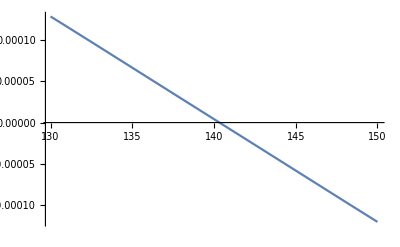

140

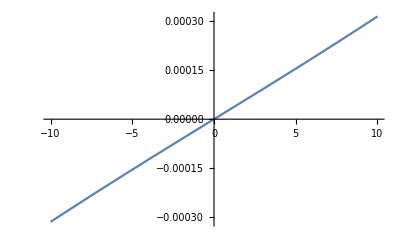

-1.24129

3.06475

2.469

```mathematica
radFld[transportAssembly, "b", {10, 0, 0}]
xarr = Table[x,{x,130,150,1}];
f=Table[radFld[transportAssembly,"bx", {x,0,0}], {x,xarr}];
ListLinePlot[Flatten/@Transpose[{xarr,f}]]
(*f=Interpolation[Flatten/@Transpose[{xarr,f}]];*)
zind= Position[Abs[f],Min[Abs[f]]][[1,1]];
zero=xarr[[zind]]
Plot[radFld[transportAssembly,"bz", {zero,0,z}],{z,-10,10}]
grx=( f[[zind+1]]-f[[zind-1]])/(xarr[[zind+1]]-xarr[[zind-1]])*10^5
grz=(radFld[transportAssembly,"bz", {zero,0,1}]-radFld[transportAssembly,"bz", {zero,0,-1}])/2*10^5
aspect = -grz/grx
```